# Teoría de Autómatas y Lenguajes Formales

## Clase 5b - AFN-ϵ en Mathematica

Profesor: Tomás de Camino Beck, Ph.D.

tomas.decamino@gmail.com

## Programación de AFN-ϵ en Mathematica

Un autómata Sencillo que acepta cualquier combinación de 0 y 1. Aunque el autómata es trivial, es un buen ejemplo simplemente para hacer fácil entender la computación de strings en un AFN-ϵ. Este ejemplo es fácil de hacer a mano y por tanto comparar con el resultado del código.

Sea δ,

```mathematica
δ=Association[
{0,"0"}->{0},
{0,ϵ}->{1},
{1,ϵ}->{2},
{1,"1"}->{1},
{2,"0"}->{2},
{2,"1"}->{2}
]
```

<|{0,0}→{0},{0,ϵ}→{1},{1,ϵ}→{2},{1,1}→{1},{2,0}→{2},{2,1}→{2}|>

Noten que para definir el autómata, se definen explícitamente las transiciones Epsilon “ϵ”.  Está implícito que hay  transiciones ϵ en los self-loops, que no hace falta incluir en la función δ. Para hacer el grafo del autómata, utilizamos el siguiente código,

```mathematica
ShowGraphFA[edges_,states_List,q0_,q_List,edgelabels_]:=Graph[
edges,
VertexSize->0.25,
VertexLabels->Placed["Name",Center],
VertexStyle->Join[{0->White},Map[(#->Red)&,q]],
EdgeWeight->edgelabels,
EdgeLabels->"EdgeWeight"
]
```

El grafo del autómata,

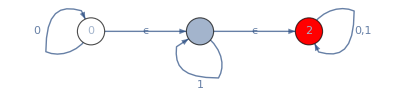

```mathematica
ShowGraphFA[{0->0,0->1,1->1,1->2,2->2},{0,1,2},{0},{2},{"0","ϵ","1","ϵ","0,1"}]
```

### Clausura ϵ

Primero construimos la función de “Clausura” (“Closure” en inglés),

```mathematica
Closure[δ_,state_List]:=Union[Map[Flatten[Most[NestWhileList[Union@@Table[δ[{#1[[i]],ϵ}],{i,Length[#1]}]&,{#},!MissingQ[#]&]]]&,state]//Flatten]
```

Noten como se utiliza la función NestWhileList, para poder mapear desde un conjunto de estados, a todos los estados accesibles a través de transiciones Epsilon “ϵ”. Noten como la condición de parada del While es cuando no se encuentra una llave y retorna Missing Lo demás es similar a la función  para autómatas no-determinísticos.

Así por ejemplo la clausura ϵ del estado 0 sería,

```mathematica
Closure[δ,{0}]
```

{0,1,2}

### Función extendida

Así ahora definimos la función DeltaHatEpsilon,

```mathematica
DeltaHatEpsilon[δ_,q0_List,string_]:=FoldList[Closure[δ,Union@@Table[δ[{#1[[i]],#2}]/._Missing->Nothing,{i,Length[#1]}]]&,Closure[δ,q0],Characters[string]]
```

probemos el string “0111”,

```mathematica
DeltaHatEpsilon[δ,{0},"0111"]
```

{{0,1,2},{0,1,2},{1,2},{1,2},{1,2}}

Como ejercicio de comprobación, realice el cómputo a mano.

## Reto

Hacer una función para eliminar las transiciones ϵ